```mathematica
H=(A/2 Exp[I  x t]-A/2 Exp[- I  x t]+1)^5
```

(1-1/2 A ⅇ^(-ⅈ t x)+1/2 A ⅇ^(ⅈ t x))^5

```mathematica
FullSimplify[Abs[H],Assumptions->0<t && 0<x && 0<A && A∈ Reals]
```

(1+Re[A Sin[t x]]^2)^(5/2)

```mathematica
Subscript[ψ, 0][t]=0;
Subscript[ψ, 1][t]=t;
Subscript[ψ, 2][t]=-t;
Subscript[ψ, 3][t]=2t;
Subscript[ψ, 4][t]=-2t;
Subscript[ψ, 5][t]=3t;
Subscript[ψ, 6][t]=-3t;
Subscript[ψ, 7][t]=4t;
Subscript[ψ, 8][t]=-4t;
Subscript[ψ, 9][t]=5t;
Subscript[ψ, 10][t]=-5t;


Subscript[f, 1][t]=Coefficient[Expand[t^2 H],ⅇ^(ⅈ Subscript[ψ, 1][t] x)];
Subscript[f, 2][t]=Coefficient[Expand[t^2 H],ⅇ^(ⅈ Subscript[ψ, 2][t] x)];
Subscript[f, 3][t]=Coefficient[Expand[t^2 H],ⅇ^(ⅈ Subscript[ψ, 3][t] x)];
Subscript[f, 4][t]=Coefficient[Expand[t^2 H],ⅇ^(ⅈ Subscript[ψ, 4][t] x)];
Subscript[f, 5][t]=Coefficient[Expand[t^2 H],ⅇ^(ⅈ Subscript[ψ, 5][t] x)];
Subscript[f, 6][t]=Coefficient[Expand[t^2 H],ⅇ^(ⅈ Subscript[ψ, 6][t] x)];
Subscript[f, 7][t]=Coefficient[Expand[t^2 H],ⅇ^(ⅈ Subscript[ψ, 7][t] x)];
Subscript[f, 8][t]=Coefficient[Expand[t^2 H],ⅇ^(ⅈ Subscript[ψ, 8][t] x)];
Subscript[f, 9][t]=Coefficient[Expand[t^2 H],ⅇ^(ⅈ Subscript[ψ, 9][t] x)];
Subscript[f, 10][t]=Coefficient[Expand[t^2 H],ⅇ^(ⅈ Subscript[ψ, 10][t] x)];
Subscript[f, 0][t]=Simplify[t^2 H-Sum[ Subscript[f, i][t] ⅇ^(ⅈ Subscript[ψ, i][t] x),{i,1,10}]]
```

1/8 (8-40 A^2+15 A^4) t^2

```mathematica
Do[Subscript[I, i]=((Subscript[f, i][t] ⅇ^(ⅈ Subscript[ψ, i][t] x))/(I x D[Subscript[ψ, i][t],t])/.t->1)-((Subscript[f, i][t] ⅇ^(ⅈ Subscript[ψ, i][t] x))/(I x D[Subscript[ψ, i][t],t])/.t->0),{i,1,10}]
```

```mathematica
II=Sum[Subscript[I, i],{i,1,10}]
```

(ⅈ (-(5 A)/2+(15 A^3)/4-(5 A^5)/16) ⅇ^(-ⅈ x))/x-(ⅈ ((5 A)/2-(15 A^3)/4+(5 A^5)/16) ⅇ^(ⅈ x))/x+(ⅈ ((5 A^2)/2-(5 A^4)/4) ⅇ^(-2 ⅈ x))/(2 x)-(ⅈ ((5 A^2)/2-(5 A^4)/4) ⅇ^(2 ⅈ x))/(2 x)+(ⅈ (-(5 A^3)/4+(5 A^5)/32) ⅇ^(-3 ⅈ x))/(3 x)-(ⅈ ((5 A^3)/4-(5 A^5)/32) ⅇ^(3 ⅈ x))/(3 x)+(5 ⅈ A^4 ⅇ^(-4 ⅈ x))/(64 x)-(5 ⅈ A^4 ⅇ^(4 ⅈ x))/(64 x)-(ⅈ A^5 ⅇ^(-5 ⅈ x))/(160 x)-(ⅈ A^5 ⅇ^(5 ⅈ x))/(160 x)

```mathematica
FullSimplify[II,Assumptions->Assumptions->0<t && 0<x && 0<A && A∈ Reals]
```

-(ⅈ A Cos[x] (600-1000 A^2+89 A^4+4 A^2 (50-7 A^2) Cos[2 x]+3 A^4 Cos[4 x]+75 ⅈ A (8-4 A^2+A^2 Cos[2 x]) Sin[x]))/(120 x)

```mathematica
FullSimplify[Abs[Out[751]],Assumptions->0<t && 0<x && 0<A && A∈ Reals]
```

1/120 Abs[(A Cos[x] (600-1000 A^2+89 A^4+4 A^2 (50-7 A^2) Cos[2 x]+3 A^4 Cos[4 x]+75 ⅈ A (8-4 A^2+A^2 Cos[2 x]) Sin[x]))/x]

```mathematica
Limit[Out[751],x->∞]
```

0

```mathematica
Integrate[1/8 (8-40 A^2+15 A^4) t^2,{t,0,1}]
```

1/3-(5 A^2)/3+(5 A^4)/8

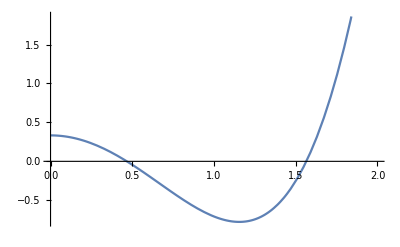

```mathematica
Plot[1/3-(5 A^2)/3+(5 A^4)/8,{A,0,2}]
```

```mathematica
Collect[Expand[H],Exp[I x t]]
```

```mathematica
1-5 A^2+(15 A^4)/8+2I((5 A)/2-(15 A^3)/4+(5 A^5)/16) Sin[x t]+2((5 A^2)/2-(5 A^4)/4) Cos[2 x t]+2 I((5 A^3)/4-(5 A^5)/32) Sin[ 3 x t]+2 5/16 A^4 Cos[4 x t]+2 I 1/32 A^5 Sin[ 5  x t]
```

1-5 A^2+(15 A^4)/8+2 ((5 A^2)/2-(5 A^4)/4) Cos[2 t x]+5/8 A^4 Cos[4 t x]+2 ⅈ ((5 A)/2-(15 A^3)/4+(5 A^5)/16) Sin[t x]+2 ⅈ ((5 A^3)/4-(5 A^5)/32) Sin[3 t x]+1/16 ⅈ A^5 Sin[5 t x]

```mathematica
1-5 A^2+(15 A^4)/8+2((5 A)/2-(15 A^3)/4+(5 A^5)/16) Sin[ xt]+2((5 A^2)/2-(5 A^4)/4)Cos[2 x t]+2((5 A^3)/4-(5 A^5)/32) Sin[3 x t]+2 5/16 A^4 Cos[x t]+2 1/32 A^5 Sin[5 x t]
```

```mathematica
Series[Out[872]/.x->1/ϵ,{ϵ,0,1}]
```

1-5 A^2+(15 A^4)/8-5/2 A ⅇ^(-(ⅈ t)/ϵ)+15/4 A^3 ⅇ^(-(ⅈ t)/ϵ)-5/16 A^5 ⅇ^(-(ⅈ t)/ϵ)+5/2 A ⅇ^((ⅈ t)/ϵ)-15/4 A^3 ⅇ^((ⅈ t)/ϵ)+5/16 A^5 ⅇ^((ⅈ t)/ϵ)+5/2 A^2 ⅇ^(-(2 ⅈ t)/ϵ)-5/4 A^4 ⅇ^(-(2 ⅈ t)/ϵ)+5/2 A^2 ⅇ^((2 ⅈ t)/ϵ)-5/4 A^4 ⅇ^((2 ⅈ t)/ϵ)-5/4 A^3 ⅇ^(-(3 ⅈ t)/ϵ)+5/32 A^5 ⅇ^(-(3 ⅈ t)/ϵ)+5/4 A^3 ⅇ^((3 ⅈ t)/ϵ)-5/32 A^5 ⅇ^((3 ⅈ t)/ϵ)+5/16 A^4 ⅇ^(-(4 ⅈ t)/ϵ)+5/16 A^4 ⅇ^((4 ⅈ t)/ϵ)-1/32 A^5 ⅇ^(-(5 ⅈ t)/ϵ)+1/32 A^5 ⅇ^((5 ⅈ t)/ϵ)

```mathematica
I2=1-5 A^2+(15 A^4)/8+2 ((5 A^2)/2-(5 A^4)/4) Cos[2 t x]+5/8 A^4 Cos[4 t x]+2 ⅈ ((5 A)/2-(15 A^3)/4+(5 A^5)/16) Sin[t x]+2 ⅈ ((5 A^3)/4-(5 A^5)/32) Sin[3 t x]+1/16 ⅈ A^5 Sin[5 t x]
```

1-5 A^2+(15 A^4)/8+2 ((5 A^2)/2-(5 A^4)/4) Cos[2 t x]+5/8 A^4 Cos[4 t x]+2 ⅈ ((5 A)/2-(15 A^3)/4+(5 A^5)/16) Sin[t x]+2 ⅈ ((5 A^3)/4-(5 A^5)/32) Sin[3 t x]+1/16 ⅈ A^5 Sin[5 t x]

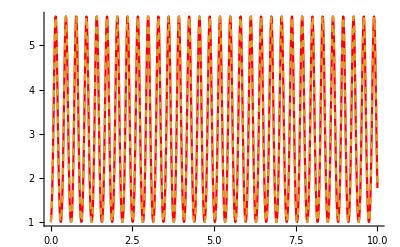

```mathematica
Plot[{Abs[H/.x->10/.A->1],(1+Re[A Sin[t x]]^2)^(5/2)/.x->10/.A->1},{t,0,10},PlotStyle->{Red,Dashed}]
```

```mathematica
I2/.x->10/.A->1
```

-17/8+5/8 Cos[10 t]+5/2 Cos[20 t]+35/16 Sin[30 t]+1/16 Sin[50 t]-(15 Sin[xt])/8

```mathematica
ExExpand[H]
```

```mathematica
(1-5 A^2+(15 A^4)/8)-5/2 A ⅇ^(-ⅈ t x)+15/4 A^3 ⅇ^(-ⅈ t x)-5/16 A^5 ⅇ^(-ⅈ t x)+5/2 A ⅇ^(ⅈ t x)-15/4 A^3 ⅇ^(ⅈ t x)+5/16 A^5 ⅇ^(ⅈ t x)+5/2 A^2 ⅇ^(-2 ⅈ t x)-5/4 A^4 ⅇ^(-2 ⅈ t x)+5/2 A^2 ⅇ^(2 ⅈ t x)-5/4 A^4 ⅇ^(2 ⅈ t x)-5/4 A^3 ⅇ^(-3 ⅈ t x)+5/32 A^5 ⅇ^(-3 ⅈ t x)+5/4 A^3 ⅇ^(3 ⅈ t x)-5/32 A^5 ⅇ^(3 ⅈ t x)+5/16 A^4 ⅇ^(-4 ⅈ t x)+5/16 A^4 ⅇ^(4 ⅈ t x)-1/32 A^5 ⅇ^(-5 ⅈ t x)+1/32 A^5 ⅇ^(5 ⅈ t x)
```

```mathematica
TeXForm[H]
```

\left(-\frac{1}{2} A e^{-i t x}+\frac{1}{2} A e^{i t x}+1\right)^5

```mathematica
TeXForm[(1+Re[A Sin[t x]]^2)^(5/2)]
```

\left(\Re(A \sin (t x))^2+1\right)^{5/2}

```mathematica
TeXForm[I2]
```

\frac{1}{16} i A^5 \sin (5 t x)+\frac{5}{8} A^4 \cos (4 t x)+\frac{15 A^4}{8}-5 A^2+2 i \left(\frac{5 A^5}{16}-\frac{15
   A^3}{4}+\frac{5 A}{2}\right) \sin (t x)+2 i \left(\frac{5 A^3}{4}-\frac{5 A^5}{32}\right) \sin (3 t x)+2 \left(\frac{5
   A^2}{2}-\frac{5 A^4}{4}\right) \cos (2 t x)+1

```mathematica
TrigReduce[Expand[(1+A^2 Sin[t x])^5]]
```

1/16 (16+80 A^4+30 A^8-80 A^4 Cos[2 t x]-40 A^8 Cos[2 t x]+10 A^8 Cos[4 t x]+80 A^2 Sin[t x]+120 A^6 Sin[t x]+10 A^10 Sin[t x]-40 A^6 Sin[3 t x]-5 A^10 Sin[3 t x]+A^10 Sin[5 t x])

```mathematica
1/16 (16+80 A^4+30 A^8+80 A^2 Sin[t x]+120 A^6 Sin[t x]+10 A^10 Sin[t x])
```

```mathematica
N[Expand[1/16 (16+80 A^4+30 A^8+80 A^2 Sin[t x]+120 A^6 Sin[t x]+10 A^10 Sin[t x])]]
```

1.+5. A^4+1.875 A^8+5. A^2 Sin[t x]+7.5 A^6 Sin[t x]+0.625 A^10 Sin[t x]

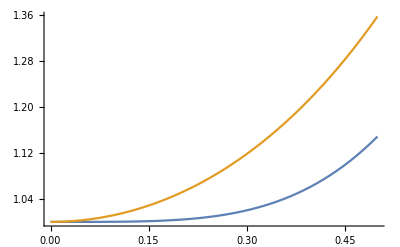

```mathematica
Plot[{(1+5 A^4+1.875 A^8+5. A^2 Sin[t x]+7.5 A^6 Sin[t x]+0.625 A^10 Sin[t x])^(1/2)/.Sin[ t x]->0,1+1.250 A^2+0.710 A^4+0.083 A^6},{A,0,.5}]
```